FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NDSolve::berr: The scaled boundary value residual error of 1.72549×10^8 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

{{y→InterpolatingFunction[{{0., 1.}}, <>]}}

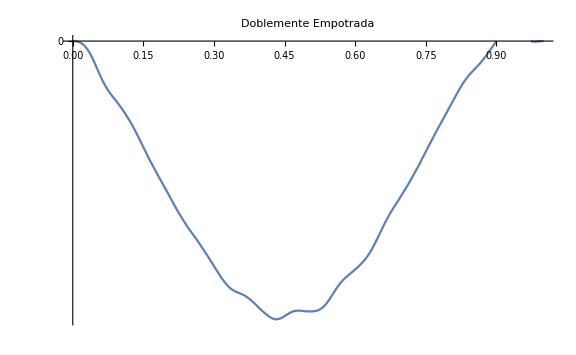

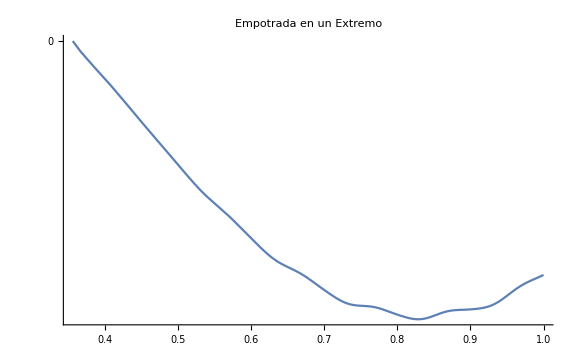

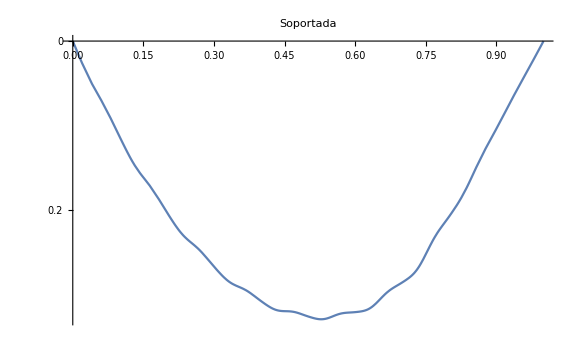

```mathematica
EI=1;
w=24;
L=1;
paso=0.1;

sol1 = NDSolve[{(15 y'[x]^2 y''[x]^3)/((1+y'[x]^2)^(7/2))-(3 y''[x]^3)/((1+y'[x]^2)^(5/2))-(9 y'[x] y''[x] Derivative[3][y][x])/((1+y'[x]^2)^(5/2))+(Derivative[4][y][x])/((1+y'[x]^2)^(3/2))==w/EI,y[0]==0,y'[0]==0,y[L]==0,y'[L]==0},y,{x,0,1},MaxSteps->1000,StartingStepSize->paso,PrecisionGoal->10,Method->{"FixedStep",Method->"ExplicitEuler"}];
sol2 = NDSolve[{(15 y'[x]^2 y''[x]^3)/((1+y'[x]^2)^(7/2))-(3 y''[x]^3)/((1+y'[x]^2)^(5/2))-(9 y'[x] y''[x] Derivative[3][y][x])/((1+y'[x]^2)^(5/2))+(Derivative[4][y][x])/((1+y'[x]^2)^(3/2))==w/EI,y[0]==0,y'[0]==0,y''[L]==0,y'''[L]==0},y,{x,0,1},MaxSteps->1000,PrecisionGoal->30,StartingStepSize->paso,Method->{"FixedStep",Method->"ExplicitEuler"}]
sol3 = NDSolve[{(15 y'[x]^2 y''[x]^3)/((1+y'[x]^2)^(7/2))-(3 y''[x]^3)/((1+y'[x]^2)^(5/2))-(9 y'[x] y''[x] Derivative[3][y][x])/((1+y'[x]^2)^(5/2))+(Derivative[4][y][x])/((1+y'[x]^2)^(3/2))==w/EI,y[0]==0,y''[0]==0,y[L]==0,y''[L]==0},y,{x,0,1},MaxSteps->1000,PrecisionGoal->10,StartingStepSize->paso,Method->{"FixedStep",Method->"ExplicitEuler"}];

f[x_]=y[x]/.sol1[[1]];
g[x_]=y[x]/.sol2[[1]];
h[x_]=y[x]/.sol3[[1]];

Plot[f[x],{x,0,1},PlotRange->{{0,1},{0,1}},ImageSize->Large, ScalingFunctions->"Reverse",PlotLabel->HoldForm[Doblemente Empotrada]]
Plot[g[x],{x,0,1},PlotRange->{{0,1},{0,1}},ImageSize->Large, ScalingFunctions->"Reverse",PlotLabel->HoldForm[Empotrada en un Extremo]]
Plot[h[x],{x,0,1},PlotRange->{{0,1},{0,1}},ImageSize->Large, ScalingFunctions->"Reverse",PlotLabel->HoldForm[Soportada]]
```